```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
spectralData={};
AppendTo[spectralData,Flatten[Import["spectral13.dat","Table"]]];
AppendTo[spectralData,Flatten[Import["spectral14.dat","Table"]]];
AppendTo[spectralData,Flatten[Import["spectral15.dat","Table"]]];
```

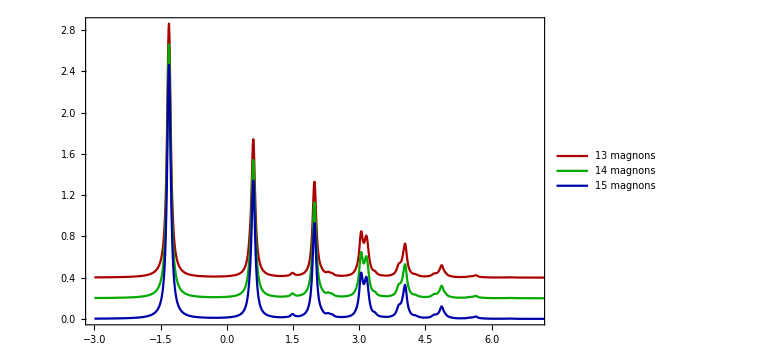

```mathematica
ListLinePlot[Table[spectralData[[it]]+0.2(Length[spectralData]-it),{it,Length[spectralData]}],PlotRange->{{-3,7},All},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},PlotLegends->{"13 magnons","14 magnons", "15 magnons"}]
```

```mathematica
spectralDataP={};
AppendTo[spectralDataP,Flatten[Import["spectral15P.dat","Table"]]];
AppendTo[spectralDataP,Flatten[Import["spectral16P.dat","Table"]]];
AppendTo[spectralDataP,Flatten[Import["spectral17P.dat","Table"]]];
```

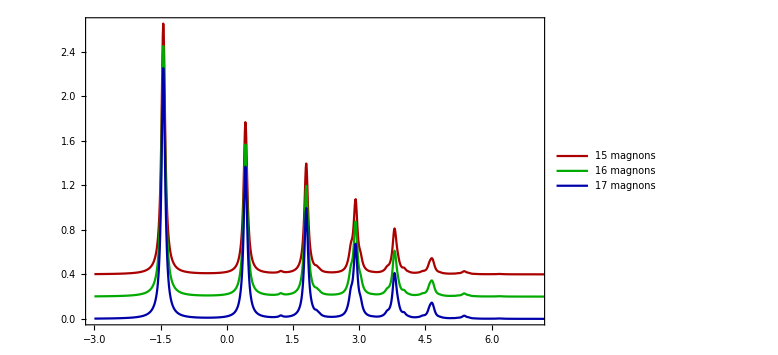

```mathematica
ListLinePlot[Table[spectralDataP[[it]]+0.2(Length[spectralDataP]-it),{it,Length[spectralDataP]}],PlotRange->{{-3,7},All},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},PlotLegends->{"15 magnons", "16 magnons", "17 magnons"}]
```

```mathematica
spectralDataAll={};
AppendTo[spectralDataAll,Flatten[Import["spectral07A_04.dat","Table"]]];
AppendTo[spectralDataAll,Flatten[Import["spectral08A_04.dat","Table"]]];
AppendTo[spectralDataAll,Flatten[Import["spectral09A_04.dat","Table"]]];
```

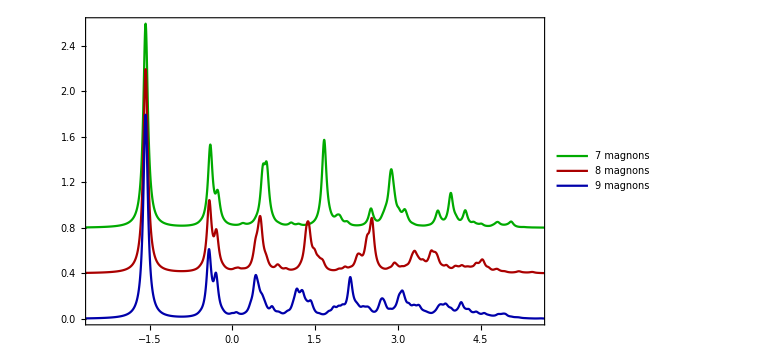

```mathematica
ListLinePlot[Table[spectralDataAll[[it]]+0.4(Length[spectralDataAll]-it),{it,Length[spectralDataAll]}],PlotRange->{{-2.5,5.5},All},DataRange->{-4,16},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Darker[Green],Darker[Red],Darker[Blue]},PlotLegends->{"7 magnons","8 magnons", "9 magnons"},AspectRatio->1/GoldenRatio]
```

```mathematica
spectralDataPlots={};
AppendTo[spectralDataPlots,Flatten[Import["spectral19A_04.dat","Table"]]];
AppendTo[spectralDataPlots,Flatten[Import["local26_04.txt","Table"]]];
AppendTo[spectralDataPlots,Flatten[Import["spectral19A_06.dat","Table"]]];
AppendTo[spectralDataPlots,Flatten[Import["local26_06.txt","Table"]]];
AppendTo[spectralDataPlots,Flatten[Import["spectral19A_08.dat","Table"]]];
AppendTo[spectralDataPlots,Flatten[Import["local26_08.txt","Table"]]];
```

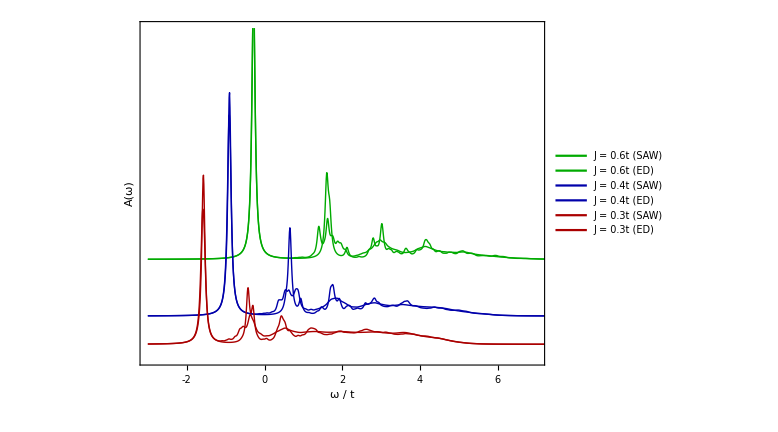

```mathematica
plt=Show[ListLinePlot[{spectralDataPlots[[5]] + 0.9, spectralDataPlots[[6]] + 0.9,spectralDataPlots[[3]] + 0.3, spectralDataPlots[[4]] + 0.3, spectralDataPlots[[1]], spectralDataPlots[[2]]},PlotRange->{{-3,7},{-0.15,3.35}},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{Darker[Green],Thin},{Darker[Green],Thick},{Darker[Blue],Thin},{Darker[Blue],Thick},{Darker[Red],Thin},{Darker[Red],Thick}},PlotLegends->Placed[{Style[ "J = 0.6t (SAW)",FontFamily->"Bookman Old Style",Black,FontSize->16],Style[ "J = 0.6t (ED)",FontFamily->"Bookman Old Style",Black,FontSize->16],Style[ "J = 0.4t (SAW)",FontFamily->"Bookman Old Style",Black,FontSize->16],Style[ "J = 0.4t (ED)",FontFamily->"Bookman Old Style",Black,FontSize->16],Style["J = 0.3t (SAW)",FontFamily->"Bookman Old Style",Black,FontSize->16],Style[ "J = 0.3t (ED)",FontFamily->"Bookman Old Style",Black,FontSize->16]},{0.84,0.82
}]],ImageSize->Large,FrameTicks->{{None,None},{Table[{i,i,0.01},{i,-2,6,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio-> 3/4,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}]
```

```mathematica
Export["fig3.pdf",plt]
```

fig3.pdf

```mathematica
spectralDataTest={};
AppendTo[spectralDataTest,Flatten[Import["spectral20A_04.dat","Table"]]];
AppendTo[spectralDataTest,Flatten[Import["spectral20A_06.dat","Table"]]];
AppendTo[spectralDataTest,Flatten[Import["spectral20A_08.dat","Table"]]];
AppendTo[spectralDataTest,Flatten[Import["spectral17A_10.dat","Table"]]];
spectralED={};
AppendTo[spectralED,Flatten[Import["local26_04.txt","Table"]]];
AppendTo[spectralED,Flatten[Import["local26_06.txt","Table"]]];
AppendTo[spectralED,Flatten[Import["local26_08.txt","Table"]]];
AppendTo[spectralED,Flatten[Import["local20_10.txt","Table"]]];
```

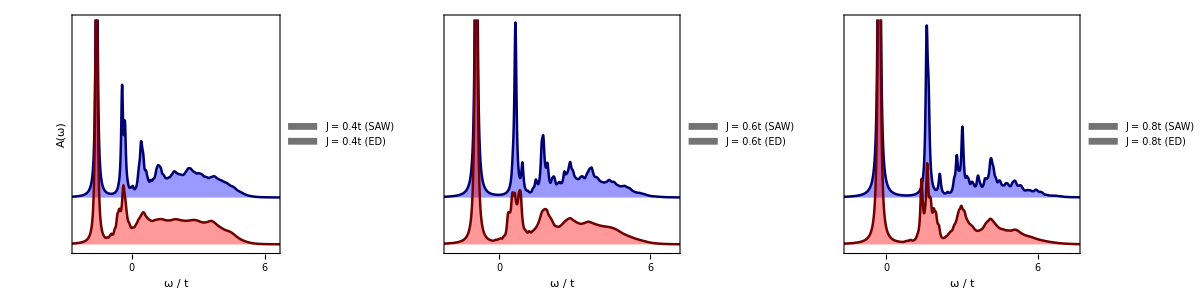

```mathematica
ar=1;
every=1;
plx=0.70;
ply=0.90;
ymax=1.2;
ymin = -ymax/50;
plotSpacing=0.25;
sawColor=Darker[Darker[Blue]];
edColor=Darker[Darker[Red]];
sawFillingColor=Blue;
edFillingColor=Red;
fillingOpacity=0.4;
lineThickness=Thickness[0.005];
legendsFontSize=20;
legend[name1_,name2_]:=SwatchLegend[{Blue,Red},{Style[ name1,FontFamily->"Bookman Old Style",Black,FontSize->legendsFontSize],Style[ name2,FontFamily->"Bookman Old Style",Black,FontSize->legendsFontSize]},LegendMarkers->Graphics[{EdgeForm[{Thick}],Opacity[0.55],Rectangle[{0,0},{1,1},RoundingRadius->0.2]}],LegendMargins->5];
plt2=Grid[{{
Show[ListLinePlot[{spectralDataTest[[1]]+plotSpacing,spectralED[[1]]},Filling->{1-> plotSpacing,2->0},FillingStyle->{1-> Directive[Opacity[fillingOpacity,sawFillingColor]],2-> Directive[Opacity[fillingOpacity,edFillingColor]]},PlotRange->{{-2.5,6.5},{ymin,ymax
}},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{sawColor,lineThickness},{edColor,lineThickness}},PlotLegends->Placed[legend["J = 0.4t (SAW)","J = 0.4t (ED)"],{plx,ply
}]],ImageSize->Medium,FrameTicks->{{None,None},{Table[{i,i,0.01},{i,-12,16,every}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio->ar,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}],
Show[ListLinePlot[{spectralDataTest[[2]]+plotSpacing,spectralED[[2]]},Filling->{1-> plotSpacing,2->0},FillingStyle->{1-> Directive[Opacity[fillingOpacity,sawFillingColor]],2-> Directive[Opacity[fillingOpacity,edFillingColor]]},PlotRange->{{-2,7},{ymin,ymax}},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{sawColor,lineThickness},{edColor,lineThickness}},PlotLegends->Placed[legend["J = 0.6t (SAW)","J = 0.6t (ED)"],{plx,ply
}]],ImageSize->Medium,FrameTicks->{{None,None},{Table[{i,i,0.01},{i,-12,16,every}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],

AspectRatio-> ar,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["",FontFamily->"Times New Roman"]}],
Show[ListLinePlot[{spectralDataTest[[3]]+plotSpacing,spectralED[[3]]},Filling->{1-> plotSpacing,2->0},FillingStyle->{1-> Directive[Opacity[fillingOpacity,sawFillingColor]],2-> Directive[Opacity[fillingOpacity,edFillingColor]]},PlotRange->{{-1.5,7.5},{ymin,ymax}},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{sawColor,lineThickness},{edColor,lineThickness}},PlotLegends->Placed[legend["J = 0.8t (SAW)","J = 0.8t (ED)"],{plx,ply
}]],ImageSize->Medium,FrameTicks->{{None,None},{Table[{i,i,0.01},{i,-12,16,every}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],

AspectRatio-> ar,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["",FontFamily->"Times New Roman"]}]
}},Spacings->0]
```

```mathematica
Export["fig1_v2.pdf",plt2]
```

fig1_v2.pdf

```mathematica
Length[spectralED[[1]]]
```

10001

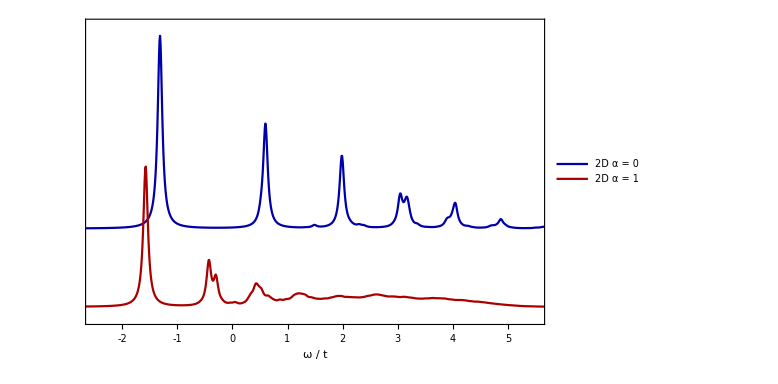

```mathematica
Show[ListLinePlot[{spectralData[[3]]+1.0,spectralDataAll[[3]]},PlotRange->{{-2.5,5.5},{-0.15,3.6}},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Darker[Blue],Darker[Red]},PlotLegends->Placed[{Style[ "2D   α = 0",FontFamily->"Arial",Black,FontSize->20],Style["2D   α = 1",FontFamily->"Arial",Black,FontSize->20]},{0.85,0.9
}]],ImageSize->Large,FrameTicks->{{None,None},{Table[{i,i,0.01},{i,-2,5,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio-> 2/3,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],None}]
```

```mathematica
spectralDataTest={};
AppendTo[spectralDataTest,Flatten[Import["SCBA.dat","Table"]]];
AppendTo[spectralDataTest,Flatten[Import["spectral22A_02.dat","Table"]]];
AppendTo[spectralDataTest,Flatten[Import["local26_02.txt","Table"]]];
```

```mathematica
labelFontSize=16;
legendLabels={Style[ "SCBA",FontFamily->"Bookman Old Style",Black,FontSize->labelFontSize],Style[ "SAW",FontFamily->"Bookman Old Style",Black,FontSize->labelFontSize],Style[ "ED",FontFamily->"Bookman Old Style",Black,FontSize->labelFontSize]};
```

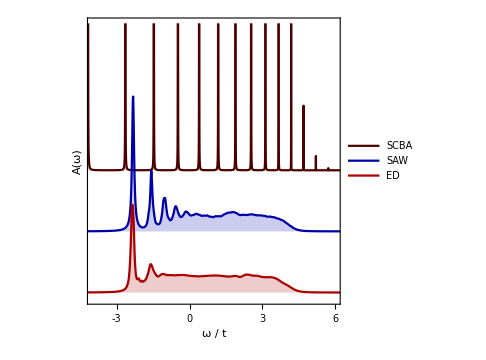

```mathematica
pt1=ListLinePlot[spectralDataTest+{1.0,0.5,0},PlotRange->{{-4,6},{-0.05,2.2}},DataRange->{-6,8},Frame->True,Axes->False,ImageSize->Medium,PlotStyle->{{Darker[Darker[Darker[Red]]]},{Darker[Blue]},{Darker[Red]}},Filling->{1->1.0,2->0.5,3->0,0},AspectRatio->1,FrameTicks->{{None,None},{Table[{i,i,0.01},{i,-6,8,1}],None}},FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],PlotLegends->Placed[LineLegend[legendLabels],{0.82,0.82}]]
```

```mathematica
Export["scba_vs_saw22_vs_ed26_J=0.2t.pdf",pt1]
```

scba_vs_saw22_vs_ed26_J=0.2t.pdf

```mathematica
spectralDataPlots={};
AppendTo[spectralDataPlots,Flatten[Import["spectralFull.dat","Table"]]];
AppendTo[spectralDataPlots,Flatten[Import["spectralNoProx.dat","Table"]]];
AppendTo[spectralDataPlots,Flatten[Import["spectralNoInt.dat","Table"]]];
AppendTo[spectralDataPlots,Flatten[Import["spectralBare.dat","Table"]]];
```

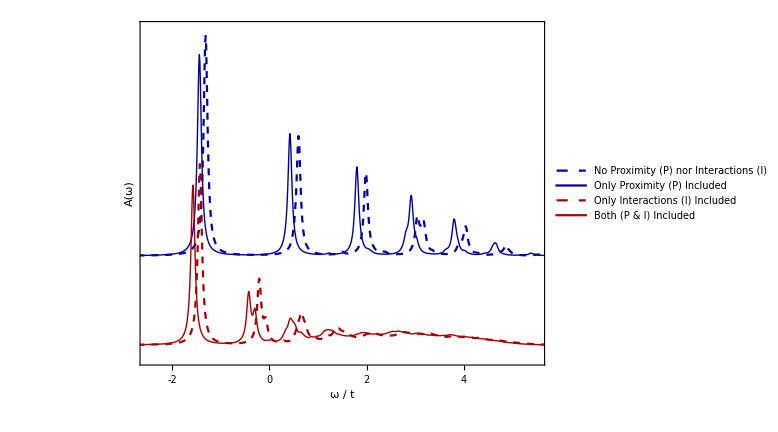

```mathematica
plt1=Show[ListLinePlot[{spectralDataPlots[[4]] + 1, spectralDataPlots[[3]] + 1, spectralDataPlots[[2]], spectralDataPlots[[1]]},PlotRange->{{-2.5,5.5},{-0.15,3.55}},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{Darker[Blue],Dashed},{Darker[Blue],Thick},{Darker[Red],Dashed},{Darker[Red],Thick}},PlotLegends->Placed[{Style[ "No Proximity (P)  nor Interactions (I)",FontFamily->"Bookman Old Style",Black,FontSize->16],Style[ "Only Proximity (P) Included",FontFamily->"Bookman Old Style",Black,FontSize->16],Style["Only Interactions (I) Included",FontFamily->"Bookman Old Style",Black,FontSize->16],Style[ "Both (P & I) Included",FontFamily->"Bookman Old Style",Black,FontSize->16]},{0.68,0.85
}]],ImageSize->Large,FrameTicks->{{None,None},{Table[{i,i,0.01},{i,-2,6,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio-> 3/4,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}]
```

```mathematica
Export["Fig2.pdf",plt1]
```

Fig2.pdf

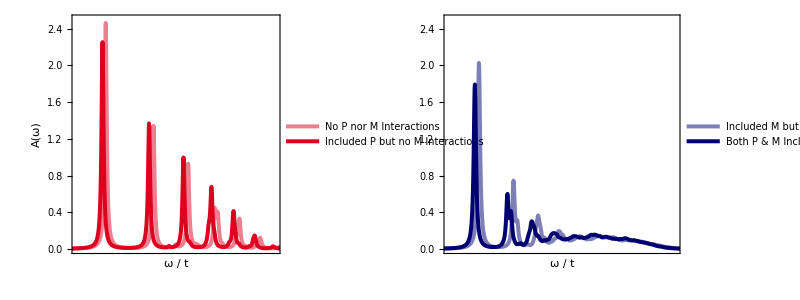

```mathematica
labelFontSize=16;
legendLabels={Style[ "No P nor M\nInteractions",FontFamily->"Bookman Old Style",Black,FontSize->labelFontSize],Style[ "Included P\nbut no M\nInteractions",FontFamily->"Bookman Old Style",Black,FontSize->labelFontSize],Style["Included M\nbut no P\nInteractions",FontFamily->"Bookman Old Style",Black,FontSize->labelFontSize],Style[ "Both P & M\nIncluded",FontFamily->"Bookman Old Style",Black,FontSize->labelFontSize]};
plotColors={Darker[Darker[Blue]],Blend[{Red,Purple},1/4]};
plt1v2=Grid[{Table[Show[ListLinePlot[Table[spectralDataPlots[[jt+it]],{it,{2,1}}],PlotRange->{{-2.5,5.5},{-0,2.5}},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{Opacity[0.5,plotColors[[If[jt<1,1,2]]]],Thickness[0.008]},{plotColors[[If[jt<1,1,2]]],Thickness[0.008]}},PlotLegends->Placed[LineLegend[legendLabels[[If[jt≠0,{1,2},{3,4}]]]],If[jt==0,{0.66,0.84},{0.66,0.84
}]]],ImageSize->Medium,FrameTicks->{{Automatic,None},{Table[{i,i,0.01},{i,-100,100,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio->GoldenRatio,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],If[jt≠0,Style["A(ω)",FontFamily->"Times New Roman"]]}],{jt,{2,0}}]
},Spacings->0]
```

```mathematica
Export["fig3.pdf",plt1v2]
```

fig3.pdf

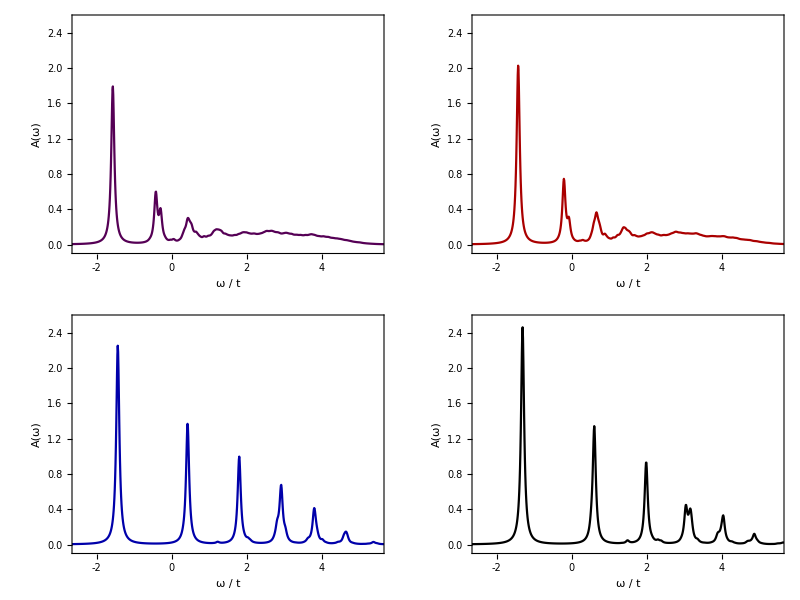

```mathematica
TableForm[{{Show[ListLinePlot[spectralDataPlots[[1]],PlotRange->{{-2.5,5.5},{-0.05,2.55}},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Darker[Purple]}],ImageSize->Medium,FrameTicks->{{Automatic,Automatic},{Table[{i,i,0.01},{i,-2,5,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio-> 1,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}],Show[ListLinePlot[spectralDataPlots[[2]],PlotRange->{{-2.5,5.5},{-0.05,2.55}},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Darker[Red]}],ImageSize->Medium,FrameTicks->{{Automatic,Automatic},{Table[{i,i,0.01},{i,-2,5,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio-> 1,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}]},{Show[ListLinePlot[spectralDataPlots[[4]],PlotRange->{{-2.5,5.5},{-0.05,2.55}},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Darker[Blue]}],ImageSize->Medium,FrameTicks->{{Automatic,Automatic},{Table[{i,i,0.01},{i,-2,5,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio->1,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}],Show[ListLinePlot[spectralDataPlots[[3]],PlotRange->{{-2.5,5.5},{-0.05,2.55}},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Black}],ImageSize->Medium,FrameTicks->{{Automatic,Automatic},{Table[{i,i,0.01},{i,-2,5,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio-> 1,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}]}}]
```

```mathematica
t=1.0;
J=0.4t;
iδ=0.05I;
Σ[ω_]:=-4t/Sqrt[3]BesselJ[7/2-ω/J,2Sqrt[3]t/J]/BesselJ[5/2-ω/J,2Sqrt[3]t/J]
A[ω_]:=-1/Pi Im[1/(ω+iδ-2J-Σ[ω+iδ])]
data=Table[A[ω],{ω,-3,8,11/1001}];
Export["SCBA.dat",data,"Table"]
```

SCBA.dat

```mathematica
spectralDataComp={};
AppendTo[spectralDataComp,Flatten[Import["SCBA.dat","Table"]]];
AppendTo[spectralDataComp,Flatten[Import["spectral20A_04.dat","Table"]]];
```

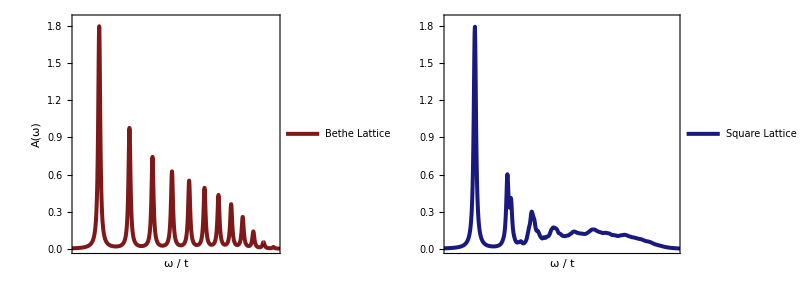

```mathematica
legendLabels={Style["Bethe    \nLattice",FontFamily->"Bookman Old Style",Black,FontSize->22],Style[ "Square   \nLattice",FontFamily->"Bookman Old Style",Black,FontSize->22]};
plotColors={Darker[Darker[Red]],Darker[Darker[Blue]]};
bethe=Grid[{Table[Show[ListLinePlot[spectralDataComp[[it]],PlotRange->{{-2.5,5.5},{-0.00,1.85}},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Opacity[0.9,plotColors[[it]]],Thickness[0.008]},PlotLegends->Placed[{legendLabels[[it]]},{0.68,0.88
}]],ImageSize->Medium,FrameTicks->{{Automatic,None},{Table[{i,i,0.01},{i,-100,100,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio->GoldenRatio,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],If[it==1,Style["A(ω)",FontFamily->"Times New Roman"]]}],{it,1,2}]
},Spacings->0]
```

```mathematica
Export["fig2_v4.pdf",bethe]
```

fig2_v4.pdf

```mathematica
lineColors={Black,Blue};
pt5=ListLinePlot[Table[spectralDataComp[[it]],{it,2}],PlotRange->{{-2,6},{0,1.85}},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->Table[{Opacity[0.6,lineColors[[it]]],Thickness[0.001]},{it,2}],Filling->Axis,AspectRatio->1/GoldenRatio,FrameTicks->{{Automatic,None},{Table[{i,i,0.01},{i,-100,100,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}]
```

-Graphics-

```mathematica
Export["saw_small_delta.pdf",pt5]
```

saw_small_delta.pdf

```mathematica
spectralDataComp={};
AppendTo[spectralDataComp,Flatten[Import["spectral16P_04_HR.dat","Table"]]];
```

```mathematica
pt6=ListLinePlot[Table[spectralDataComp[[it]],{it,2}],PlotRange->{{-2,6},{0,1.85}},DataRange->{-3,8},Frame->True,Axes->False,ImageSize->Large,PlotStyle->Table[{Opacity[0.6,lineColors[[it]]],Thickness[0.001]},{it,2}],Filling->Axis,AspectRatio->1/GoldenRatio,FrameTicks->{{Automatic,None},{Table[{i,i,0.01},{i,-100,100,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}]
```

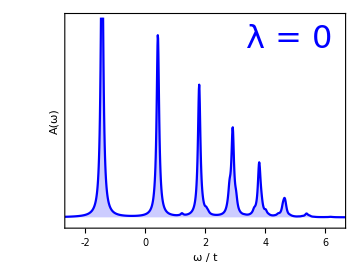
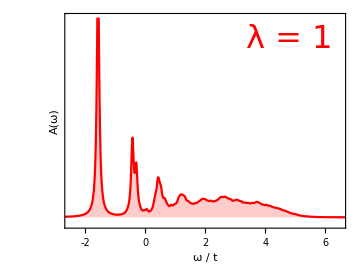

```mathematica
data={spectralDataPlots[[3]], spectralDataPlots[[1]]};
stl={{Blue},{Red}};
leg={Style[ "λ = 0",FontFamily->"Bookman Old Style",Blue,FontSize->32],Style[ "λ = 1",FontFamily->"Bookman Old Style",Red,FontSize->32]};
plts1=Table[
Show[ListLinePlot[data[[it]],PlotRange->{{-2.5,6.5},{-0.05,1.5}},DataRange->{-3,7},Frame->True,Axes->False,Filling->{1->0},ImageSize->Large,PlotStyle->stl[[it]],PlotLegends->Placed[leg[[it]],{0.8,0.88}]],ImageSize->Medium,FrameTicks->{{None,None},{Table[{i,i,0.01},{i,-2,6,1}],None}},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],AspectRatio-> 3/4,FrameLabel-> {Style["ω / t",FontFamily->"Times New Roman"],Style["A(ω)",FontFamily->"Times New Roman"]}],
{it,{1,2}}]
```